```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=BinaryReadList["test1-sigma=1_0.dat","UnsignedInteger32"];
l=Flatten@Map[Reverse@IntegerDigits[#,2,32]&,l]; (* 32-bit, LSB to MSB *)
l=N[l];
len=Length[l]
```

1048576

```mathematica
Mean[l]
StandardDeviation[N@l]
```

0.503601

0.499987

{1.,0.275005,0.164053,0.12759,0.10373,0.0909954,0.0796623,0.0723043,0.0671361,0.0620747,0.0569713,0.0533367,0.0506748,0.0487969,0.0460149,0.043416,0.0434952,0.0396411,0.0374638,0.037295,0.0360847}

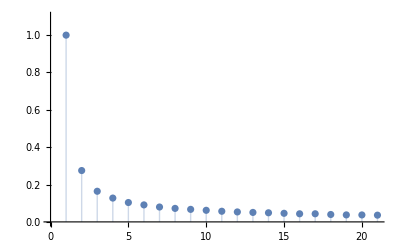

2.53574

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```